```mathematica
d:=3
l:=1
m:=0.1
Subscript[m, c]:=Sqrt[3]/2
M:= Sqrt[m^2+Subscript[m, c]^2]
a:=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
b:=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
c:=d/2
norm=Gamma[a]*Gamma[b]/((4*π)^(d/2)*l^2*Gamma[d/2]);
f[z_]:=norm*Hypergeometric2F1[a,b,c,1/2(1+Cosh[z])]
argToHue[arg_]:=Hue[(arg+Pi)/(2 Pi)];
Legended[Plot3D[Re[f[x+I y]],{x,-5,5},{y,-5,5},PlotRange->{{-5,5},{-5,5},{-0.2,0.2}},ColorFunction->Function[{x,y,z},argToHue[z]],ColorFunctionScaling->False,PlotPoints->150,Mesh->None,Lighting->"Neutral",AxesLabel->{"Re(z)","Im(z)","Re(f(z))"}],BarLegend[{Function[z,argToHue[z]],{-Pi,Pi}},	Ticks->Table[{t,ToString[TraditionalForm[t]]},{t,{-Pi,-Pi/2,0,Pi/2,Pi}}],LegendLabel->"Arg(f(z))"]]
```

-Graphics3D-

-Graphics3D-

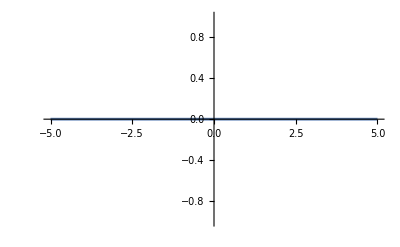

```mathematica
Plot[N[Limit[Re[norm*Hypergeometric2F1[a,b,c,1/2(1+Cosh[z])-I*ϵ]],{ϵ->0}]],{z,-5,5},PlotRange->{{-5,5},All}]
```

```mathematica
N[Limit[Re[norm*Hypergeometric2F1[a,b,c,1/2(1+Cosh[0.01])+I*ϵ]],{ϵ->0}]]
```

0.